```mathematica
(*Import Measurement Data*)
folder="/Users/ahmad/Desktop/Minicircuit 1";
sampleName="Minicircuit 1";

files=Sort@FileNames["*.txt",folder];

data=Association@Table[file->Import[file,"Table"][[2;;]],{file,files}];

(*Column Definitions*)
cols=<|"TIME"->1,"VDS"->2,"SDVDS"->3,"IDS"->4,"SDIDS"->5,"VGS"->6,"SDVGS"->7,"IGS"->8,"SDIGS"->9|>;

(*Helper Functions*)
getCurve[key_,x_,y_]:=Module[{xdata,ydata},xdata=data[key][[All,cols[x]]];
ydata=data[key][[All,cols[y]]];
If[y==="IDS"||y==="IGS",ydata=ydata/1000];
Transpose[{xdata,ydata}]];

meanValue[key_,variable_]:=Module[{value},value=Mean[data[key][[All,cols[variable]]]];
If[variable==="IDS"||variable==="IGS",value=value/1000];
value];

lastValue[key_,variable_]:=data[key][[-1,cols[variable]]];

secToLastValue[key_,variable_]:=data[key][[-2,cols[variable]]];

(*Sort Files by Mean VGS*)
sortedKeys=SortBy[Keys[data],-meanValue[#,"VGS"]&];

highCurrentFile=First[sortedKeys];

lowCurrentFile=Last[sortedKeys];

labels="\!\(\*SubscriptBox[\(V\), \(GS\)]\) = "<>ToString@NumberForm[meanValue[#,"VGS"],{4,3}]<>" V"&/@sortedKeys;

(*Inspect low-current sweeps near pinch-off*)lowCurrentKeys=Take[sortedKeys,-3];

Table[{FileNameTake[key],ScientificForm[meanValue[key,"VGS"],6],ScientificForm[Min[data[key][[All,cols["IDS"]]]],8],ScientificForm[Max[data[key][[All,cols["IDS"]]]],8],ScientificForm[Mean[data[key][[All,cols["IDS"]]]],8]},{key,lowCurrentKeys}]
VDSbias=4.0;

lowCurrentCheck=Table[Module[{curve,point},curve=Transpose[{data[key][[All,cols["VDS"]]],data[key][[All,cols["IDS"]]]}];
point=First@Nearest[curve[[All,1]]->curve,VDSbias];
{FileNameTake[key],ScientificForm[meanValue[key,"VGS"],6],ScientificForm[point[[1]],6],ScientificForm[point[[2]],10]}],{key,lowCurrentKeys}];

Grid[Prepend[lowCurrentCheck,{"File","Mean VGS (V)","Selected VDS (V)","IDS (raw units)"}],Frame->All]
(*Separate Variables*)
timeData=data/@sortedKeys/. x_:>x[[All,cols["TIME"]]];

VDSdata=data/@sortedKeys/. x_:>x[[All,cols["VDS"]]];
VDSsdData=data/@sortedKeys/. x_:>x[[All,cols["SDVDS"]]];

IDSdata=data/@sortedKeys/. x_:>x[[All,cols["IDS"]]];
IDSsdData=data/@sortedKeys/. x_:>x[[All,cols["SDIDS"]]];

VGSdata=data/@sortedKeys/. x_:>x[[All,cols["VGS"]]];
VGSsdData=data/@sortedKeys/. x_:>x[[All,cols["SDVGS"]]];

IGSdata=data/@sortedKeys/. x_:>x[[All,cols["IGS"]]];
IGSsdData=data/@sortedKeys/. x_:>x[[All,cols["SDIGS"]]];
VGSvalues=meanValue[#,"VGS"]&/@sortedKeys;

(*Summary*)
Print["Loaded ",Length[files]," files from ",sampleName];

Print["Measured \!\(\*SubscriptBox[\(V\), \(GS\)]\) range: ",NumberForm[First[VGSvalues],{4,3}]," V to ",NumberForm[Last[VGSvalues],{4,3}]," V"];
```

{{nomVGS_m1p290V.txt,-1.28997,3.358061×10^-3,3.3211428×10^-1,1.5531279×10^-1},{nomVGS_m1p350V.txt,-1.3499,1.644765×10^-3,6.3941667×10^-2,2.8789997×10^-2},{nomVGS_m1p410V.txt,-1.41004,1.027978×10^-3,1.0074411×10^-2,5.1212606×10^-3}}

File | Mean VGS (V) | Selected VDS (V) | IDS (raw units)
nomVGS_m1p290V.txt | -1.28997 | 3.99092 | 2.32463546×10^-1
nomVGS_m1p350V.txt | -1.3499 | 3.99946 | 4.8110087×10^-2
nomVGS_m1p410V.txt | -1.41004 | 4.00155 | 5.277032×10^-3

Loaded 13 files from Minicircuit 1

Measured V_GS range: -0.690 V to -1.410 V

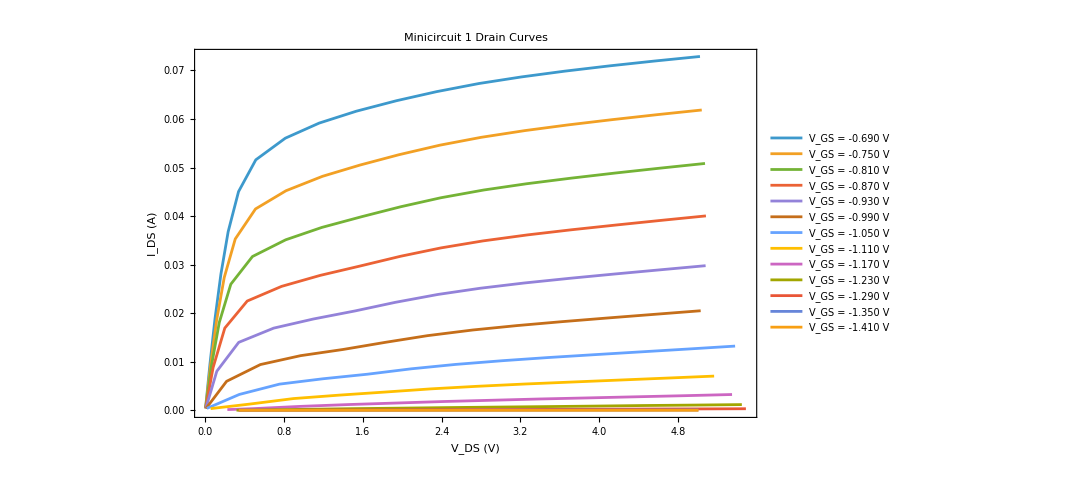

```mathematica
(* =======================================================================*)(*1. Drain Curves*)(* =======================================================================*)drainCurves=getCurve[#,"VDS","IDS"]&/@sortedKeys;

drainPlot=ListLinePlot[drainCurves,Frame->True,Axes->False,FrameLabel->{"\!\(\*SubscriptBox[\(V\), \(DS\)]\) (V)","\!\(\*SubscriptBox[\(I\), \(DS\)]\) (A)"},PlotLabel->sampleName<>" Drain Curves",PlotLegends->Placed[labels,Right],PlotRange->All,ImageSize->800];

drainPlot
```

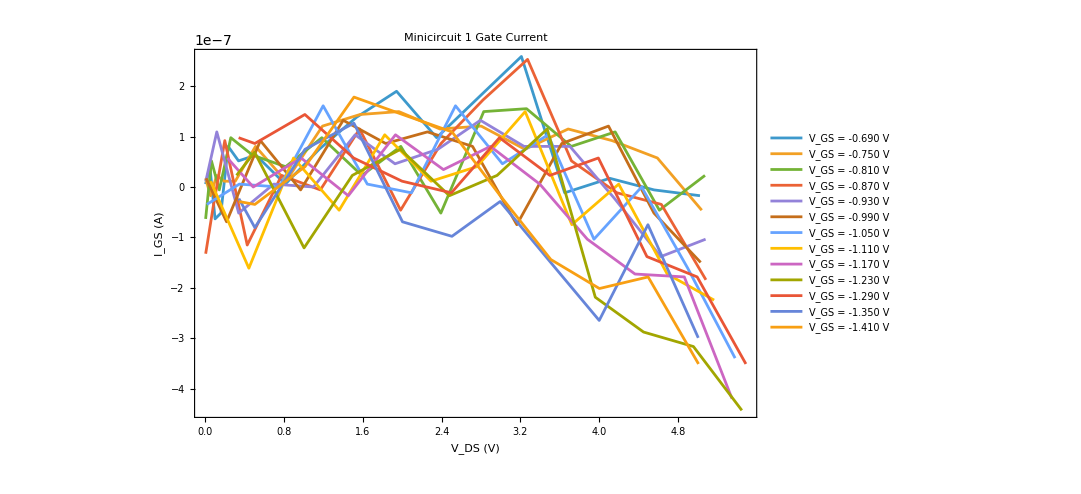

```mathematica
(* =======================================================================*)(*2. Gate Current*)(* =======================================================================*)gateCurrentCurves=getCurve[#,"VDS","IGS"]&/@sortedKeys;

gateCurrentPlot=ListLinePlot[gateCurrentCurves,Frame->True,Axes->False,FrameLabel->{"\!\(\*SubscriptBox[\(V\), \(DS\)]\) (V)","\!\(\*SubscriptBox[\(I\), \(GS\)]\) (A)"},PlotLabel->sampleName<>" Gate Current",PlotLegends->Placed[labels,Right],PlotRange->All,ImageSize->800];

gateCurrentPlot
```

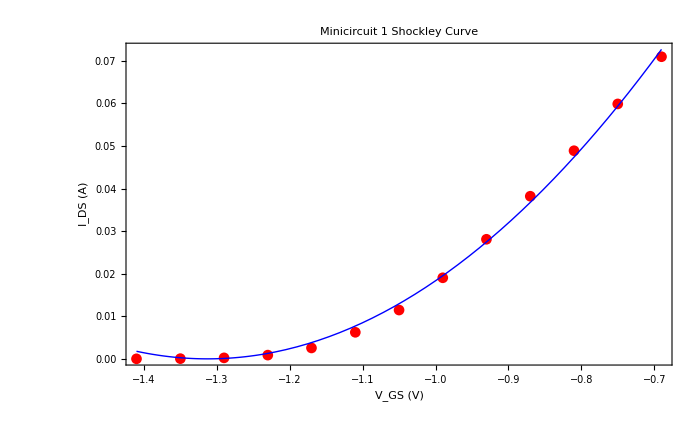

I_DSS = 323.084 mA

V_P = -1.313 V

R^2 = 0.99873

```mathematica
(* =======================================================================*)(*3. Shockley Curve*)(* =======================================================================*)VDSbias=4.0;

transferData=Table[Module[{curve,point},curve=Transpose[{data[key][[All,cols["VDS"]]],data[key][[All,cols["IDS"]]]}];
point=First@Nearest[curve[[All,1]]->curve,VDSbias];
{meanValue[key,"VGS"],point[[2]]*10^-3}],{key,sortedKeys}];

shockleyFitData=Select[transferData,NumericQ[#[[2]]]&&#[[2]]>0&];
shockleyFit=NonlinearModelFit[shockleyFitData,IDSSparameter (1-v/Vpparameter)^2,{{IDSSparameter,Max[shockleyFitData[[All,2]]]},{Vpparameter,-1.4}},v];
IDSS=IDSSparameter/. shockleyFit["BestFitParameters"];

Vp=Vpparameter/. shockleyFit["BestFitParameters"];

shockleyPlot=Show[ListPlot[shockleyFitData,PlotMarkers->Automatic,PlotStyle->Red],Plot[shockleyFit[v],{v,Min[VGSvalues],Max[VGSvalues]},PlotStyle->{Blue,Thick}],Frame->True,Axes->False,FrameLabel->{"\!\(\*SubscriptBox[\(V\), \(GS\)]\) (V)","\!\(\*SubscriptBox[\(I\), \(DS\)]\) (A)"},PlotLabel->sampleName<>" Shockley Curve",PlotRange->All,ImageSize->700];

shockleyPlot

Print["\!\(\*SubscriptBox[\(I\), \(DSS\)]\) = ",NumberForm[1000 IDSS,{7,3}]," mA"];

Print["\!\(\*SubscriptBox[\(V\), \(P\)]\) = ",NumberForm[Vp,{6,3}]," V"];

Print["\!\(\*SuperscriptBox[\(R\), \(2\)]\) = ",NumberForm[shockleyFit["RSquared"],{7,5}]];
```

```mathematica
(*Fitted current and transconductance functions*)
Clear[IDversusVGSfunction];

IDversusVGSfunction[VGS_?NumericQ]:=shockleyFit[VGS];

Subscript[g,m][VGS_?NumericQ]:=Evaluate[D[shockleyFit[x],x]/. x->VGS];
```

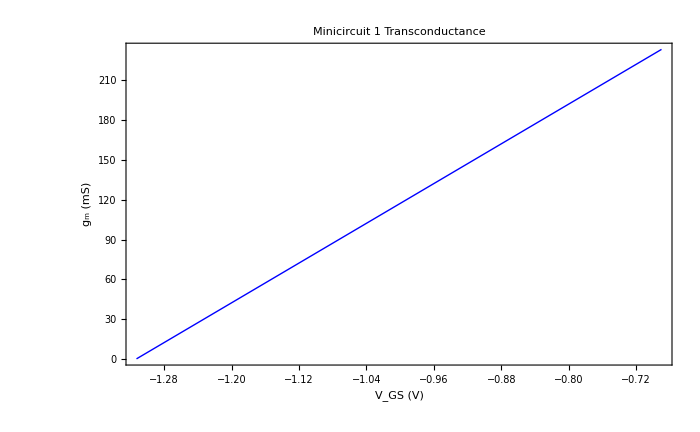

```mathematica
(* =====================================================================*)(*4. Transconductance*)(* =======================================================================*)gmPlot=Plot[1000 Subscript[g,m][VGS],{VGS,Vp,Max[VGSvalues]},Frame->True,Axes->False,FrameLabel->{"\!\(\*SubscriptBox[\(V\), \(GS\)]\) (V)","\!\(\*SubscriptBox[\(g\), \(m\)]\) (mS)"},PlotLabel->sampleName<>" Transconductance",PlotStyle->{Blue,Thick},PlotRange->All,ImageSize->700];

gmPlot
```

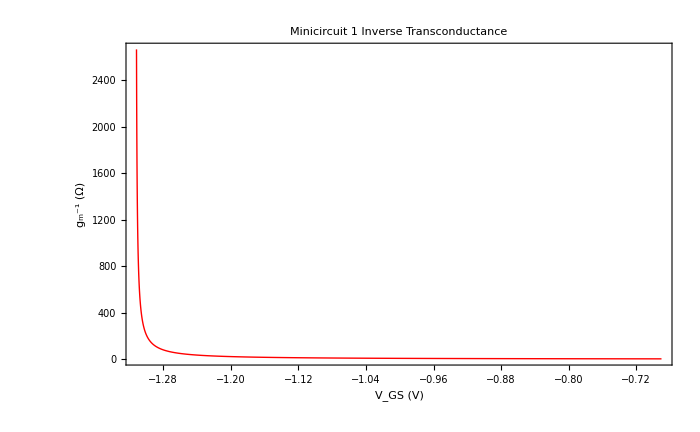

```mathematica
(* ==================================================================*)(*5. Inverse Transconductance*)(* =================================================================*)inverseGmPlot=Plot[1/Subscript[g,m][VGS],{VGS,Vp+0.001,Max[VGSvalues]},Frame->True,Axes->False,FrameLabel->{"\!\(\*SubscriptBox[\(V\), \(GS\)]\) (V)","\!\(\*SuperscriptBox[SubscriptBox[\(g\), \(m\)], \(-1\)]\) (Ω)"},PlotLabel->sampleName<>" Inverse Transconductance",PlotStyle->{Red,Thick},PlotRange->All,ImageSize->700];

inverseGmPlot
```

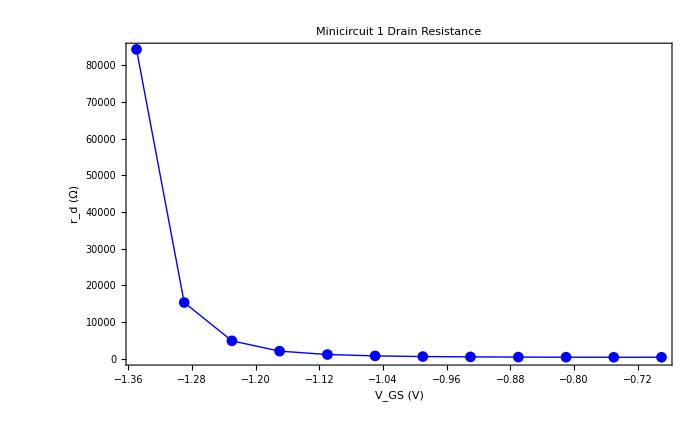

```mathematica
(* ====================================================================*)(*6. Drain Resistance*)(* =====================================================================*)rdValues=Table[Module[{curve,fitData,fitLine,slope,nFit},curve=SortBy[getCurve[key,"VDS","IDS"],First];
nFit=Max[4,Ceiling[0.25 Length[curve]]];
fitData=Take[curve,-nFit];
fitLine=LinearModelFit[fitData,x,x];
slope=Coefficient[Normal[fitLine],x];
If[NumericQ[slope]&&slope>0,1/slope,Indeterminate]],{key,sortedKeys}];

rdMaximum=100000;    (*100 kΩ*)

rdData=Select[Transpose[{VGSvalues,rdValues}],NumericQ[#[[2]]]&&Positive[#[[2]]]&&#[[2]]<rdMaximum&];

rdfunction=Interpolation[SortBy[rdData,First],InterpolationOrder->1];

rdPlot=ListLinePlot[rdData,Frame->True,Axes->False,PlotMarkers->Automatic,FrameLabel->{"\!\(\*SubscriptBox[\(V\), \(GS\)]\) (V)","\!\(\*SubscriptBox[\(r\), \(d\)]\) (Ω)"},PlotLabel->sampleName<>" Drain Resistance",PlotStyle->{Blue,Thick},PlotRange->All,ImageSize->700];

rdPlot
```

```mathematica
(*Transistor-model inputs for source-follower design*)
fit=shockleyFit;

rdVGSFunction=rdfunction;

VpFit=Vp;

IDSSFit=IDSS;
```

## Source Follower Design

### Source Follower self - bias design

```mathematica
(* ============================================================*)(*JFET Self-Bias Source Follower Design*)(* ===========================================================*)Clear[JFETSelfBiasSourceFollowerDesign];

JFETSelfBiasSourceFollowerDesign[RF_,VDS_,ID_,Rsource_,RL_,beta_,fit_,rdVGSFunction_,VpFit_,IDSSFit_,f0_,PrintResults_:True]:=Module[{VDD,RS,RG,VGS,VG,VS,VD,gmValue,rdValue,VoltageGain,Zin,Zout,Cgate,Csource,ChannelNoise,PDC},(*Check the selected current*)If[ID<=0||ID>=IDSSFit,Return["Selected drain current must satisfy 0 < ID < IDSS."]];
(*Find VGS from the fitted transfer characteristic*)VGS=x/. FindRoot[fit[x]==ID,{x,0.9 VpFit,VpFit,0}];
(*Small-signal transistor parameters*)gmValue=D[fit[x],x]/. x->VGS;
rdValue=If[NumberQ[rdVGSFunction],rdVGSFunction,rdVGSFunction[VGS]];
(*Self-bias operating point*)VG=0;
VS=-VGS/beta;
RS=VS/ID;
RG=Rsource;
VD=VDS+VS;
VDD=VD+ID RF;
(*Source-follower voltage gain*)VoltageGain=gmValue/(gmValue+1/RS+(1+RF/RS)/rdValue);
(*Input and output impedance*)Zin=RG;
Zout=1/(1/RS+(1+gmValue rdValue)/(RF+rdValue));
(*Coupling capacitors*)Cgate=10/(2 Pi f0 (RG+Rsource));
Csource=10/(2 Pi f0 (Zout+RL));
(*FET channel-noise density at 4.2 K*)ChannelNoise=Sqrt[4*1.380649*10^-23*4.2*(2/(3 gmValue))];
(*Total DC supply power*)PDC=VDD ID;
If[PrintResults,Print[Style["JFET Self-Bias Source Follower Design",14,Bold]];
Print["\!\(\*SubscriptBox[\(I\), \(D\)]\) = ",NumberForm[1000 ID,{7,3}]," mA    ","\!\(\*SubscriptBox[\(V\), \(DS\)]\) = ",NumberForm[VDS,{6,3}]," V"];
Print["\!\(\*SubscriptBox[\(V\), \(GS\)]\) = ",NumberForm[VGS,{7,3}]," V    ","\!\(\*SubscriptBox[\(V\), \(S\)]\) = ",NumberForm[VS,{7,3}]," V    ","\!\(\*SubscriptBox[\(V\), \(D\)]\) = ",NumberForm[VD,{7,3}]," V"];
Print["\!\(\*SubscriptBox[\(R\), \(S\)]\) = ",NumberForm[RS,{8,1}]," Ω    ","\!\(\*SubscriptBox[\(R\), \(G\)]\) = ",NumberForm[RG,{9,1}]," Ω"];
Print["\!\(\*SubscriptBox[\(V\), \(DD\)]\) = ",NumberForm[VDD,{7,3}]," V"];
Print["\!\(\*SubscriptBox[\(g\), \(m\)]\) = ",NumberForm[1000 gmValue,{7,3}]," mS    ","1/\!\(\*SubscriptBox[\(g\), \(m\)]\) = ",NumberForm[1/gmValue,{8,2}]," Ω    ","\!\(\*SubscriptBox[\(r\), \(d\)]\) = ",NumberForm[rdValue,{9,1}]," Ω"];
Print["\!\(\*SubscriptBox[\(A\), \(V\)]\) = ",NumberForm[VoltageGain,{7,4}],"  (",NumberForm[20 Log[10,Abs[VoltageGain]],{7,3}]," dB)"];
Print["\!\(\*SubscriptBox[\(Z\), \(in\)]\) = ",NumberForm[Zin,{9,1}]," Ω    ","\!\(\*SubscriptBox[\(Z\), \(out\)]\) = ",NumberForm[Zout,{8,2}]," Ω"];
Print["\!\(\*SubscriptBox[\(C\), \(gate\)]\) = ",NumberForm[10^12 Cgate,{8,2}]," pF    ","\!\(\*SubscriptBox[\(C\), \(source\)]\) = ",NumberForm[10^12 Csource,{8,2}]," pF"];
Print["FET channel noise at 4.2 K = ",NumberForm[10^9 ChannelNoise,{7,4}]," nV/\!\(\*SqrtBox[\(Hz\)]\)"];
Print["\!\(\*SubscriptBox[\(P\), \(DC\)]\) = ",NumberForm[1000 PDC,{7,3}]," mW"];];
{VDD,(*1*)RS,(*2*)RG,(*3*)VGS,(*4*)VG,(*5*)VS,(*6*)VD,(*7*)gmValue,(*8*)rdValue,(*9*)VoltageGain,(*10*)Zin,(*11*)Zout,(*12*)Cgate,(*13*)Csource,(*14*)ChannelNoise,(*15*)PDC              (*16*)}];
```

```mathematica
(* ========================================================*)(*Source Follower Design Values*)(* ===============================================================*)VDSSourceFollower=1.0;          (*V*)

IDSourceFollower=1.19*10^-3;    (*A*)

RF=50;                          (*Ohm*)

RSignal=10000;                  (*Ohm*)

RLoad=50;                       (*Ohm*)

f0=25.6*10^6;                   (*Hz*)

beta=1.0;
```

```mathematica
Design1=JFETSelfBiasSourceFollowerDesign[RF,VDSSourceFollower,IDSourceFollower,RSignal,RLoad,beta,fit,rdVGSFunction,VpFit,IDSSFit,f0,True];
```

JFET Self-Bias Source Follower Design

I_D = 1.190 mA    V_DS = 1.000 V

V_GS = -1.233 V    V_S = 1.233 V    V_D = 2.233 V

R_S = 1036.1 Ω    R_G = 10000 Ω

V_DD = 2.293 V

g_m = 29.875 mS    1/g_m = 33.47 Ω    r_d = 5435.8 Ω

A_V = 0.9627  (-0.330 dB)

Z_in = 10000 Ω    Z_out = 32.52 Ω

C_gate = 3.11 pF    C_source = 753.39 pF

FET channel noise at 4.2 K = 0.0719 nV/√Hz

P_DC = 2.728 mW

### Source Follower Self - bias operation

```mathematica
(* ==========================================================*)(*JFET Self-Bias Source Follower Operation*)(* ===============================================*)Clear[JFETSelfBiasSourceFollowerOperation];

JFETSelfBiasSourceFollowerOperation[VDD_,RF_,RG_,RS_,RL_,fit_,rdVGSFunction_,VpFit_,IDSSFit_,PrintResults_:True]:=Module[{ID,VGS,VG,VS,VD,VDS,gmValue,rdValue,VoltageGain,Zin,Zout,ChannelNoise,PDC},VG=0;
(*Solve the self-bias operating point*)VS=v/. FindRoot[v==RS fit[-v],{v,-0.9 VpFit,0,-VpFit}];
VGS=VG-VS;
ID=fit[VGS];
If[ID<=0||ID>=IDSSFit,Return["Calculated drain current is outside 0 < ID < IDSS."]];
VD=VDD-ID RF;
VDS=VD-VS;
(*Small-signal transistor parameters*)gmValue=D[fit[x],x]/. x->VGS;
rdValue=If[NumberQ[rdVGSFunction],rdVGSFunction,rdVGSFunction[VGS]];
(*Source-follower performance*)VoltageGain=gmValue/(gmValue+1/RS+(1+RF/RS)/rdValue);
Zin=RG;
Zout=1/(1/RS+(1+gmValue rdValue)/(RF+rdValue));
(*FET channel-noise density at 4.2 K*)ChannelNoise=Sqrt[4*1.380649*10^-23*4.2*(2/(3 gmValue))];
(*DC supply power*)PDC=VDD ID;
If[PrintResults,Print[Style["JFET Self-Bias Source Follower Operation",14,Bold]];
Print["\!\(\*SubscriptBox[\(I\), \(D\)]\) = ",NumberForm[1000 ID,{7,3}]," mA    ","\!\(\*SubscriptBox[\(V\), \(DS\)]\) = ",NumberForm[VDS,{7,3}]," V"];
Print["\!\(\*SubscriptBox[\(V\), \(GS\)]\) = ",NumberForm[VGS,{7,3}]," V    ","\!\(\*SubscriptBox[\(V\), \(G\)]\) = ",NumberForm[VG,{6,3}]," V    ","\!\(\*SubscriptBox[\(V\), \(S\)]\) = ",NumberForm[VS,{7,3}]," V"];
Print["\!\(\*SubscriptBox[\(V\), \(D\)]\) = ",NumberForm[VD,{7,3}]," V"];
Print["\!\(\*SubscriptBox[\(g\), \(m\)]\) = ",NumberForm[1000 gmValue,{7,3}]," mS    ","1/\!\(\*SubscriptBox[\(g\), \(m\)]\) = ",NumberForm[1/gmValue,{8,2}]," Ω    ","\!\(\*SubscriptBox[\(r\), \(d\)]\) = ",NumberForm[rdValue,{9,1}]," Ω"];
Print["\!\(\*SubscriptBox[\(A\), \(V\)]\) = ",NumberForm[VoltageGain,{7,4}],"  (",NumberForm[20 Log[10,Abs[VoltageGain]],{7,3}]," dB)"];
Print["\!\(\*SubscriptBox[\(Z\), \(in\)]\) = ",NumberForm[Zin,{9,1}]," Ω    ","\!\(\*SubscriptBox[\(Z\), \(out\)]\) = ",NumberForm[Zout,{8,2}]," Ω"];
Print["FET channel noise at 4.2 K = ",NumberForm[10^9 ChannelNoise,{7,4}]," nV/\!\(\*SqrtBox[\(Hz\)]\)"];
Print["\!\(\*SubscriptBox[\(P\), \(DC\)]\) = ",NumberForm[1000 PDC,{7,3}]," mW"];];
{ID,(*1*)VDS,(*2*)VGS,(*3*)VG,(*4*)VS,(*5*)VD,(*6*)gmValue,(*7*)rdValue,(*8*)VoltageGain,(*9*)Zin,(*10*)Zout,(*11*)ChannelNoise,(*12*)PDC              (*13*)}];
```

```mathematica
VDDSourceFollower= Design1[[1]];

RSSourceFollower= Design1[[2]];

RGSourceFollower= Design1[[3]];
```

```mathematica
Operation1=JFETSelfBiasSourceFollowerOperation[VDDSourceFollower,RF,RGSourceFollower,RSSourceFollower,RLoad,fit,rdVGSFunction,VpFit,IDSSFit,True];
```

JFET Self-Bias Source Follower Operation

I_D = 1.190 mA    V_DS = 1.000 V

V_GS = -1.233 V    V_G = 0 V    V_S = 1.233 V

V_D = 2.233 V

g_m = 29.875 mS    1/g_m = 33.47 Ω    r_d = 5435.8 Ω

A_V = 0.9627  (-0.330 dB)

Z_in = 10000 Ω    Z_out = 32.52 Ω

FET channel noise at 4.2 K = 0.0719 nV/√Hz

P_DC = 2.728 mW